```mathematica
SetDirectory["~/Library/AFS@Reed/emcmanis/Thesis/TeX/Thesis Template/Figures"]
```

/afs/reed.edu/user/e/m/emcmanis/Thesis/TeX/Thesis Template/Figures

### Constants

```mathematica
h = 6.626*10^(-34); (*J s*)
hbar = h/(2π);
e=-1.602*10^(-19); (* C *)
ϵ0=8.854*10^(-12); (* C^2/(J m) *)
me=9.109*10^(-31); (*kg*)
mp=1.673*10^(-27); (*kg*)
μ=(mp/(me+mp))*me;
a0=(4π ϵ0 hbar^2)/(μ e^2);
```

### Bohr hydrogen energies

```mathematica
Ens=Table[-hbar^2/(a0^2 2 μ n^2)*1/(1.602*10^(-19)),{n,1,10}]
```

{-13.5941,-3.39852,-1.51045,-0.84963,-0.543763,-0.377613,-0.27743,-0.212408,-0.167828,-0.135941}

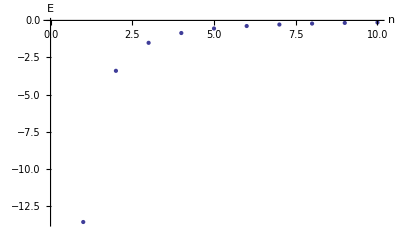

```mathematica
ListPlot[Ens, PlotRange->Full,AxesLabel->{"n", "E"}]
```

### Hydrogen Wave Functions

```mathematica
?LaguerreL
```

LaguerreL[n,x] gives the Laguerre polynomial L_n(x). 
LaguerreL[n,a,x] gives the generalized Laguerre polynomial L_n^a(x).

```mathematica
psi[n_,ρ_]:=(*Sqrt[(2/(n a0))^3 ((n-1)!)/(2n(n!)^3)] -- wiki norm*)(√2)/n ⅇ^-(ρ/ n)*LaguerreL[n-1,1,2*ρ/n]
```

```mathematica
LaguerreL[n-1,1,2*ρ/n]/.{ρ->0,n->1}
```

1

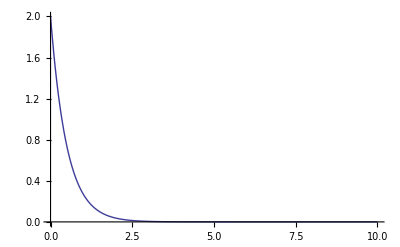

```mathematica
Plot[psi[1,r]^2,{r,0,10},PlotRange->All]
```

```mathematica
Integrate[psi[1,r]^2,{r,0,∞}]
```

1

```mathematica
a0
```

5.29582×10^-11

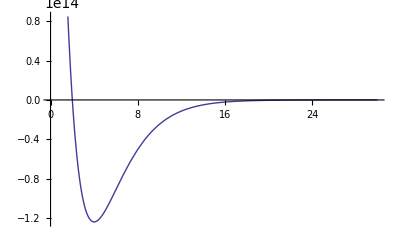

```mathematica
Plot[psi[2,r],{r,0,30}]
```

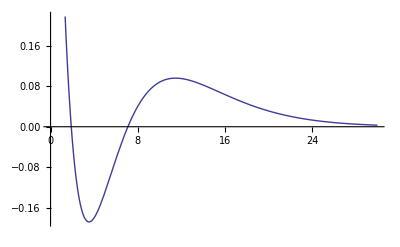

```mathematica
Plot[psi[3,r],{r,0,30}]
```

```mathematica
Integrate[psi[1,r]^2,{r,0,∞}]
```

1

```mathematica
Integrate[psi[2,r]^2,{r,0,∞}]
```

1

```mathematica
Integrate[psi[10,r]^2,{r,0,∞}]
```

1

#### test

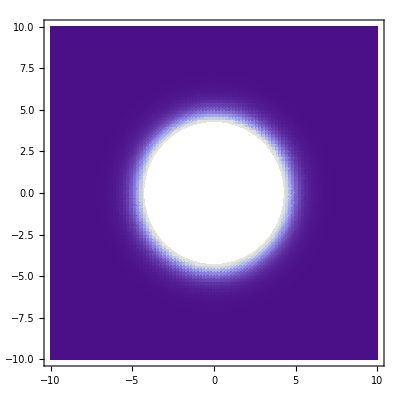

```mathematica
Table[DensityPlot[(0.5*psi[n,Sqrt[x^2+y^2]])^2,{x,-10,10},{y,-10,10},PlotPoints->100],{n,1,1}]
```

```mathematica
?DensityPlot
```

DensityPlot[f,{x,x_min,x_max},{y,y_min,y_max}] makes a density plot of f as a function of x and y.

#### actual file saving part

```mathematica
SetDirectory["~/Desktop/Ellen/Thesis/TeX/Thesis Template/Figures"]
```

/Network/Servers/Knowlton.local/Users/zphantom/Desktop/Ellen/Thesis/TeX/Thesis Template/Figures

```mathematica
Export["densityplots.png",Table[DensityPlot[psi[n,Sqrt[x^2+y^2]]^2,{x,-7,7},{y,-7,7}],{n,1,6}]]
```

densityplots.png

### Hydrogen V_eff

```mathematica
V[r_]:=n^2/2*1/r^2 - 1/r
```

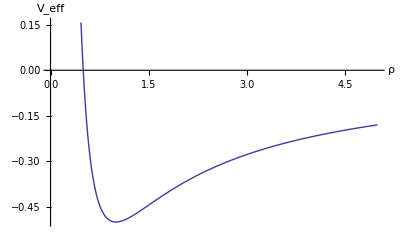

```mathematica
Plot[V[r]/.{n->1},{r,0,5},AxesLabel->{"ρ","V_eff"}]
```

### Yukawa Cutoff

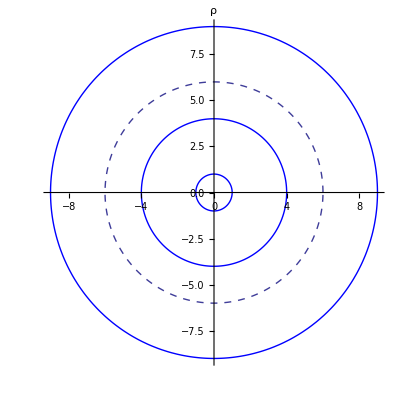

```mathematica
Show[PolarPlot[{1,4,9},{th,0,2π},PlotStyle->Blue,AxesLabel->"ρ"],PolarPlot[6,{th,0,2π},PlotStyle->Dashed]]
```

### Yukawa Veff

```mathematica
V[r_]:=n^2/2*1/r^2 - 1/r*ⅇ^(-r/l)
```

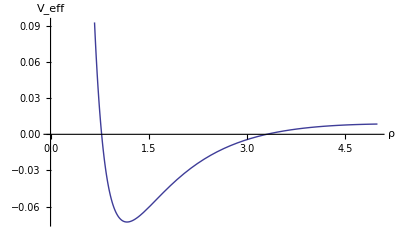

```mathematica
Plot[V[r]/.{n->1,l->1.75},{r,0,5},AxesLabel->{"ρ","V_eff"}]
```

## Numeric Wave Functions

#### Large Yukawa

```mathematica
λ=200;
```

```mathematica
dρ=0.1;
ρinf=Round[20*λ];
nn=Round[ρinf/dρ];
```

```mathematica
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
```

```mathematica
valvecs200=Eigensystem[H,-100];
```

```mathematica
sorted=Sort[valvecs200[[1]]]
```

{-0.00487541,-0.00301651,-0.00178452,-0.00097922,-0.000472414,-0.00017815,-0.0000359636,4.60923×10^-7,2.73965×10^-6,7.0553×10^-6,0.0000132512,0.0000212167,0.000030878,0.0000421828,0.0000550911,0.0000695714,0.0000855979,0.000103149,0.000122206,0.000142753,0.000164776,0.000188262,0.0002132,0.00023958,0.000267393,0.00029663,0.000327283,0.000359345,0.000392809,0.00042767,0.000463922,0.000501559,0.000540576,0.000580969,0.000622732,0.000665863,0.000710356,0.000756209,0.000803417,0.000851977,0.000901887,0.000953142,0.00100574,0.00105968,0.00111496,0.00117157,0.00122951,0.00128878,0.00134939,0.00141132,0.00147457,0.00153914,0.00160503,0.00167225,0.00174077,0.00181062,0.00188177,0.00195424,0.00202802,0.0021031,0.00217949,0.00225719,0.00233619,0.0024165,0.00249811,0.00258101,0.00266522,0.00275072,0.00283752,0.00292562,0.00301501,0.00310569,0.00319767,0.00329094,0.0033855,0.00348135,0.00357849,0.00367692,0.00377663,0.00387763,0.00397992,0.00408349,0.00418834,0.00429448,0.0044019,0.0045106,0.00462058,0.00473185,0.00484439,0.00495821,0.00507331,0.00518969,0.00530735,0.00542628,0.00554649,0.00566797,0.00579073,0.00591476,0.00604007,0.00616665}

```mathematica
Position[valvecs200[[1]],sorted[[6]]]
```

{{85}}

```mathematica
Table[{i,1./i^2},{i,1,20}]
```

{{1,1.},{2,0.25},{3,0.111111},{4,0.0625},{5,0.04},{6,0.0277778},{7,0.0204082},{8,0.015625},{9,0.0123457},{10,0.01},{11,0.00826446},{12,0.00694444},{13,0.00591716},{14,0.00510204},{15,0.00444444},{16,0.00390625},{17,0.00346021},{18,0.00308642},{19,0.00277008},{20,0.0025}}

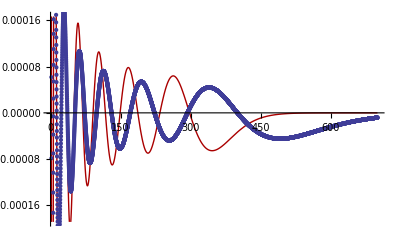

```mathematica
Show[Plot[1/150 psi[14,r],{r,0,700},PlotStyle->{Darker[Red],Thick}], ListPlot[Table[{i/10, 10/i valvecs200[[2,85,i]]},{i,1,7000}]]]
```

```mathematica
Integrate[psi[2,r]^2,{r,0,∞}]
```

2

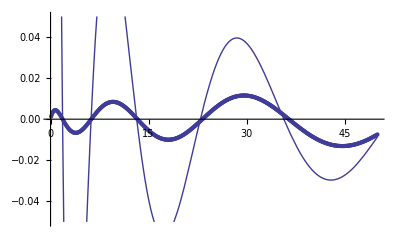

```mathematica
Show[Plot[psi[11,r],{r,0,50},PlotRange->{-0.05,0.05}], ListPlot[Table[{i/10, valvecs[[2,48,i]]},{i,1,500}]]]
```

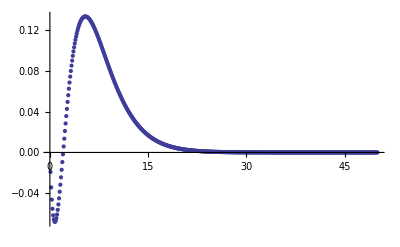

```mathematica
ListPlot[Table[{i/10, valvecs[[2,72,i]]},{i,1,500}],PlotRange->Full]
```

#### A scattering state becomes a bound state

λ = 12.5 (scattering), ρinf = 20*λ

```mathematica
λ=14;
```

```mathematica
dρ=0.1;
ρinf=Round[20*λ];
nn=Round[ρinf/dρ];
```

```mathematica
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
```

```mathematica
valvecs3=Eigensystem[H,-100];
```

```mathematica
valvecs0[[1,100]]
```

0.0000793164

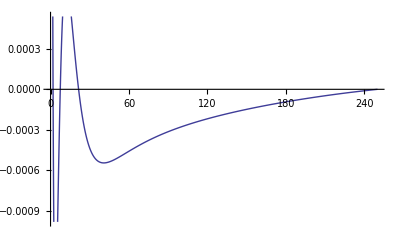

```mathematica
ListPlot[Table[{i/10, 10/i valvecs0[[2,100,i]]},{i,1,Length[valvecs0[[2,100]]]}],Joined->True]
```

λ = 12.9 (scattering)

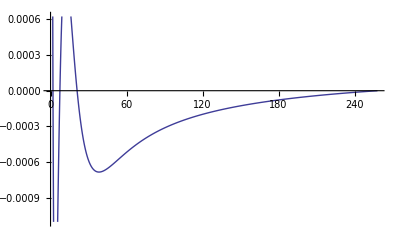

```mathematica
ListPlot[Table[{i/10,10/i valvecs[[2,100,i]]},{i,1,Length[valvecs[[2,100]]]}],Joined->True]
```

λ = 13.1 (bound)

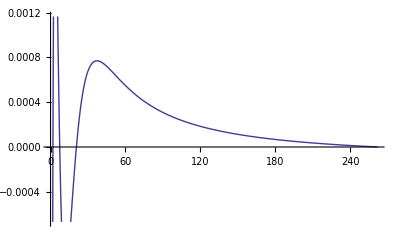

```mathematica
ListPlot[Table[{i/10, 10/i valvecs2[[2,100,i]]},{i,1,Length[valvecs2[[2,100]]]}],Joined->True]
```

λ=14 (bound)

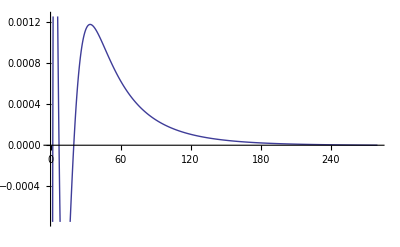

```mathematica
ListPlot[Table[{i/10, 10/i valvecs3[[2,99,i]]},{i,1,Length[valvecs3[[2,99]]]}],Joined->True]
```

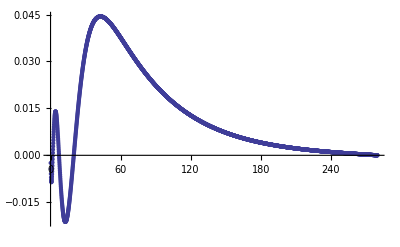
```mathematica
a=-Graphics-
```

-Graphics-

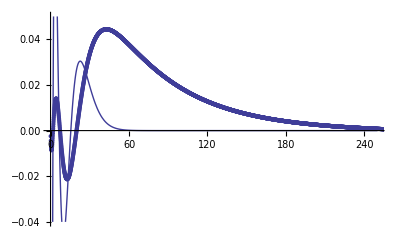

```mathematica
Show[Plot[-1/2 psi[4,r],{r,0,250},PlotRange->{-0.04,0.05}],a]
```

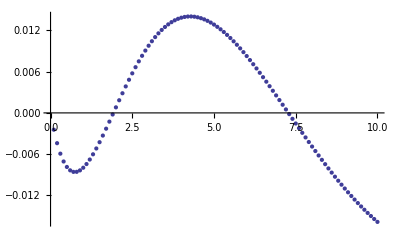

```mathematica
ListPlot[Table[{i/10, valvecs3[[2,99,i]]},{i,1,100}]]
```

#### The Importance of dρ

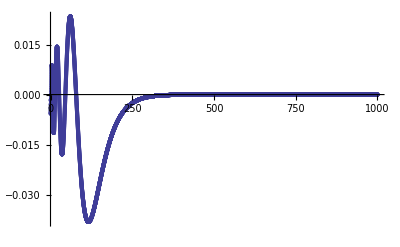

```mathematica
ListPlot[Table[{i/10, valvecs50[[2,93,i]]},{i,1,Length[valvecs50[[2,93]]]}],PlotRange->Full]
```

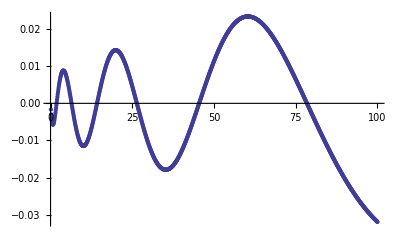

```mathematica
ListPlot[Table[{i/10, valvecs50[[2,93,i]]},{i,1,1000}]]
```

#### The Importance of ρinf

12.5, scattering

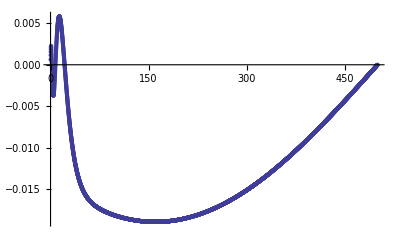

```mathematica
ListPlot[Table[{i/10, bigvalvecs0[[2,100,i]]},{i,1,Length[bigvalvecs0[[2,100]]]}]]
```

12.9, *bound*

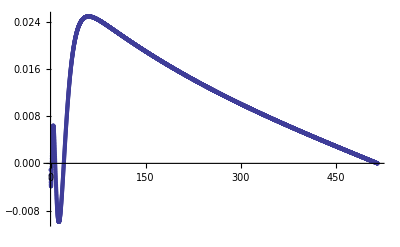

```mathematica
ListPlot[Table[{i/10, bigvalvecs[[2,100,i]]},{i,1,Length[bigvalvecs[[2,100]]]}]]
```

#### Plots for old things (λ=10)

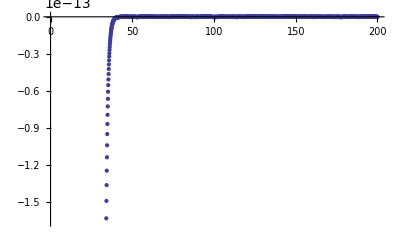

```mathematica
ListPlot[Table[{i/10, valvecs[[2,43,i]]},{i,1,Length[valvecs[[2,43]]]}]]
```

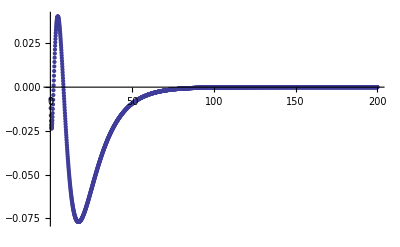

```mathematica
ListPlot[Table[{i/10, valvecs[[2,96,i]]},{i,1,Length[valvecs[[2,96]]]}],PlotRange->Full]
```

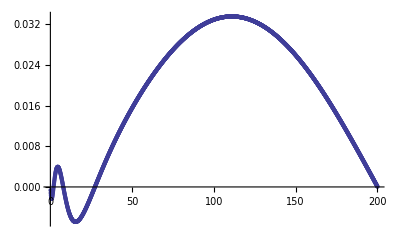

```mathematica
ListPlot[Table[{i/10, valvecs[[2,100,i]]},{i,1,Length[valvecs[[2,100]]]}],PlotRange->Full]
```

#### n = 2 bound states

```mathematica
λ=20;
```

```mathematica
dρ=0.1;
ρinf=Round[20*λ];
nn=Round[ρinf/dρ];
```

```mathematica
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
```

```mathematica
valvecs=Eigensystem[H,-150];
```

```mathematica
sorted=Sort[valvecs[[1]]]
```

{-0.901151,-0.163391,-0.0386787,-0.00617771,0.0000102392,0.000185522,0.000524666,0.00101988,0.00166517,0.00245646,0.00339078,0.00446578,0.00567958,0.00703062,0.0085176,0.0101394,0.0118951,0.0137839,0.0158051,0.0179581,0.0202423,0.0226572,0.0252023,0.0278774,0.0306819,0.0336157,0.0366783,0.0398695,0.043189,0.0466367,0.0502122,0.0539154,0.057746,0.061704,0.0657891,0.0700011,0.07434,0.0788056,0.0833977,0.0881163,0.0929611,0.0979321,0.103029,0.108252,0.113601,0.119076,0.124677,0.130403,0.136255,0.142232,0.148335,0.154562,0.160916,0.167394,0.173998,0.180726,0.18758,0.194559,0.201662,0.208891,0.216244,0.223722,0.231325,0.239052,0.246904,0.254881,0.262982,0.271208,0.279558,0.288033,0.296632,0.305355,0.314203,0.323175,0.332272,0.341492,0.350837,0.360306,0.369899,0.379616,0.389458,0.399423,0.409512,0.419726,0.430063,0.440525,0.45111,0.461819,0.472652,0.483609,0.49469,0.505894,0.517223,0.528675,0.540251,0.55195,0.563773,0.57572,0.587791,0.599985,0.612303,0.624744,0.637309,0.649998,0.66281,0.675746,0.688805,0.701987,0.715293,0.728723,0.742276,0.755952,0.769752,0.783675,0.797721,0.811891,0.826184,0.8406,0.85514,0.869803,0.884589,0.899498,0.914531,0.929687,0.944966,0.960368,0.975893,0.991541,1.00731,1.02321,1.03923,1.05537,1.07163,1.08802,1.10453,1.12116,1.13791,1.15479,1.1718,1.18892,1.20617,1.22354,1.24103,1.25865,1.27639,1.29425,1.31223,1.33034,1.34857,1.36692}

```mathematica
Position[valvecs[[1]],sorted[[2]]]
```

{{99}}

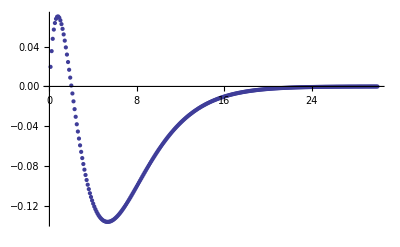

```mathematica
yuk=ListPlot[Table[{i/10, valvecs[[2,99,i]]},{i,1,300}],PlotRange->Full]
```

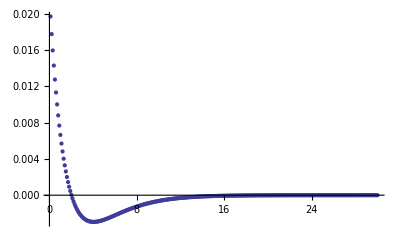

```mathematica
yukpsi=ListPlot[Table[{i/10, valvecs[[2,99,i]]/i},{i,1,300}],PlotRange->Full]
```

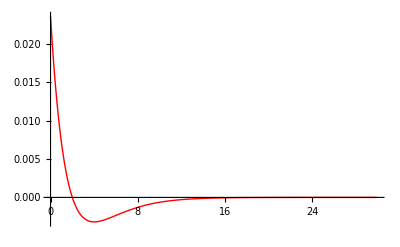

```mathematica
hydpsi=Plot[1/60 psi[2,r],{r,0,30},PlotRange->Full,PlotStyle->{Red,Thick}]
```

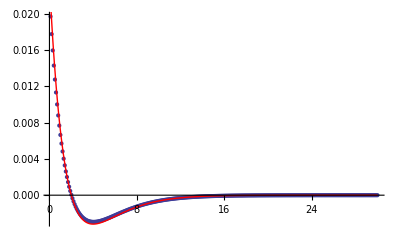

```mathematica
Show[yukpsi,hydpsi]
```

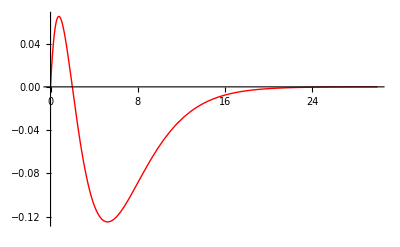

```mathematica
hyd=Plot[1/7 r*psi[2,r],{r,0,30},PlotRange->Full,PlotStyle->{Red,Thick}]
```

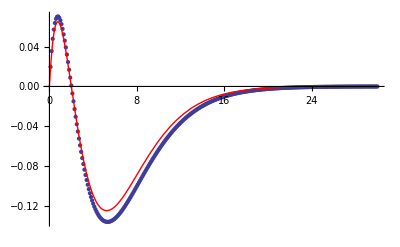

```mathematica
Show[yuk,hyd]
```